# Network 2 & Network 3 for shoe

## 48x48

Set Environment

```mathematica
root = "~/";
```

```mathematica
root = "Y:/";
```

```mathematica
root = "\\\\5.185.152.91\\research\\";
```

Generate network 2

## Construct network

```mathematica
rdata=ReadList[root<>"/shoe/32/net2_raw.txt",{Number,Number,Real,Real,Real,Real,Real,Real}];Length[rdata]
```

20098

```mathematica
rgood = Select[rdata, #[[2]]>1000&];Dimensions[rgood]
```

{6023,8}

```mathematica
rgood[[All,5]]=Sqrt[rgood[[All,5]]]/(Abs[rgood[[All,8]]]);
rgood[[All,3]]=Sqrt[rgood[[All,3]]]/(Abs[rgood[[All,8]]]+1);
rgood[[All,4]]=Sqrt[rgood[[All,4]]]/(Abs[rgood[[All,8]]]+1);
```

```mathematica
rselected=Select[rgood,Total[#[[3;;5]]]<1.2&&Quotient[#[[1]],10000]≠Mod[#[[1]],10000]&];
```

```mathematica
g2=Graph[Map[Quotient[#[[1]],10000]<->Mod[#[[1]],10000]&,rselected],VertexLabels->"Name"];
```

```mathematica
Length[rselected]
```

50

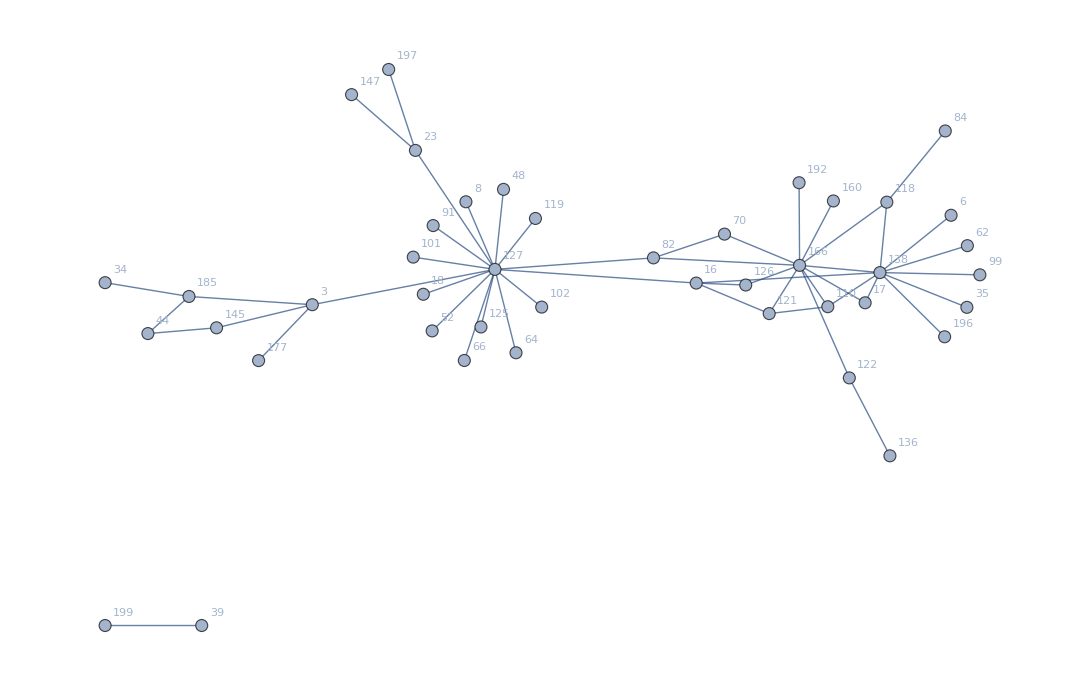

```mathematica
g2
```

## Export Network2

```mathematica
Export[root<>"/shoe/32/net2_el.txt",EdgeList[g2]]
```

\\5.185.152.91\research\/shoe/32/net2_el.txt

Construct network 3

## Load network 3

```mathematica
el=Map[#[[1]]<->#[[2]]&,ReadList[root<>"/shoe/net3_el_03_02.txt",{Number,Number}]];
```

```mathematica
g3 = Graph[el,VertexLabels->"Name"];
VertexCount[g3]
EdgeCount[g3]
```

40

33

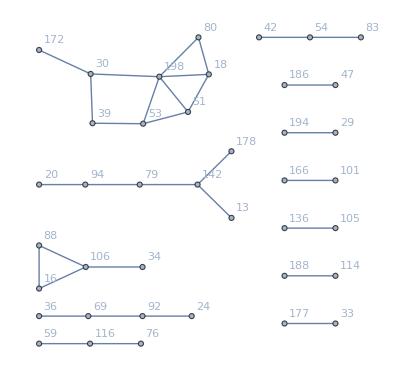

```mathematica
g3
```